```mathematica
Needs["ErrorBarPlots`"]
```

## Bosted fit R_FF

```mathematica
Q2=1.51
z=Sqrt[Q2]
tau=Q2/(4*0.938^2)
GEbosted= 1/(1+0.62*z+0.68*z^2+2.80*z^3+0.83*z^4)
GMbosted=2.7972*(1/(1+0.35*z+2.44*z^2+0.50*z^3+1.04*z^4+0.34*z^5))
Rffbosted=2.7972*GEbosted/GMbosted
RffPT=1-0.12*Q2
```

1.51

1.22882

0.429053

0.101249

0.298649

0.948319

0.8188

```mathematica
deltabosted= ((2.7972*GEbosted)^2-(GMbosted*RffPT)^2)/(RffPT^2+tau*2.7972^2)
R2gammabosted=1+ ((2*deltabosted*(1-eps))/(GMbosted^2+(eps/tau)*GEbosted^2))
```

0.0050686

1+(0.0101372 (1-eps))/(0.0891913+0.0238931 eps)

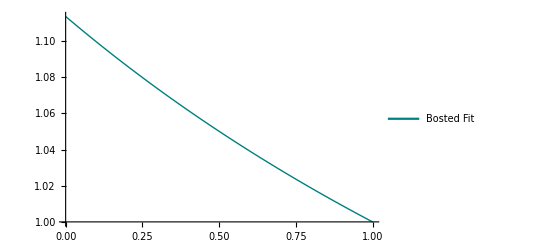

```mathematica
Pboosted=Plot[R2gammabosted,{eps,0,1},PlotStyle->{Blend[{Green,Blue}],Thick},PlotLegends-> Placed[LineLegend[{"Bosted Fit"}],{0.75,0.85}],LabelStyle->Directive[FontFamily->"Arial",Bold,FontSize->14]]
```

## Arrington Fit R_FF

```mathematica
x=Q2
GEarr=1/(1+3.226*x+1.508*x^2-0.3773*x^3+0.611*x^4-0.185*x^5+(1.596*10^-2)*x^6)
GMarr=2.7972*(1/(1+3.19*x+1.355*x^2+0.151*x^3-1.14*10^-2*x^4+5.33*10^-4x^5-9*10^-6x^6))
Rffarrington= 2.7972*GEarr/GMarr
```

1.51

0.100766

0.298491

0.944288

```mathematica
deltaarr =((2.7972*GEarr)^2-(GMarr*RffPT)^2)/(RffPT^2+tau*2.7972^2)
R2gammaarr=1+ ((2*deltaarr*(1-eps))/(GMarr^2+(eps/tau)*GEarr^2))
```

0.00489448

1+(0.00978896 (1-eps))/(0.089097+0.0236654 eps)

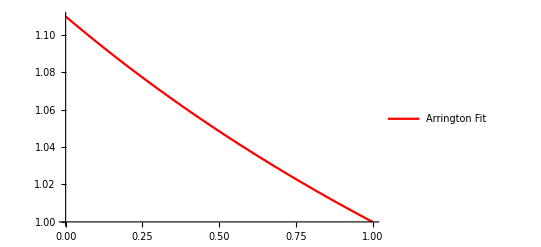

```mathematica
Parrington=Plot[R2gammaarr,{eps,0,1},PlotStyle->{Red},PlotLegends-> Placed[LineLegend[{"Arrington Fit"}],{0.75,0.75}],LabelStyle->Directive[FontFamily->"Arial",Bold,FontSize->14]]
```

## Pade Model

```mathematica
a1=3.439
a2=-1.602
a3=0.068
b1=15.055
b2=48.061
b3=99.304
b4=0.012
b5=8.650
c1=-1.465
c2=1.260
c3=0.262
d1=9.627
d2=0.000
d3=0.000
d4=11.179
d5=13.245
```

3.439

-1.602

0.068

15.055

48.061

99.304

0.012

8.65

-1.465

1.26

0.262

9.627

0.

0.

11.179

13.245

0.0900458

0.306156

0.429053

0.8188

0.000149137

1+(0.000298273 (1-eps))/(0.0937318+0.018898 eps)

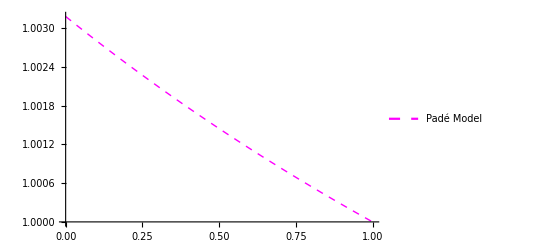

```mathematica
GEpade= (1+a1*tau+a2*tau^2+a3*tau^3)/(1+b1*tau+b2*tau^2+b3*tau^3+b4*tau^4+b5*tau^5)
GMpade= 2.7972*((1+c1*tau+c2*tau^2+c3*tau^3)/(1+d1*tau+d2*tau^2+d3*tau^3+d4*tau^4+d5*tau^5))
tau=Q2/(4*0.938^2)
RffPT=1-0.12*Q2
deltaBern=((2.7972*GEpade)^2-(GMpade*RffPT)^2)/(RffPT^2+tau*2.7972^2)
R2gammaBern=1+ ((2*deltaBern*(1-eps))/(GMpade^2+(eps/tau)*GEpade^2))
PltBernauer=Plot[R2gammaBern,{eps,0,1},PlotStyle->{Magenta,Dashed,Thick},PlotLegends-> Placed[LineLegend[{"Padé Model"}],{0.75,0.65}],LabelStyle->Directive[FontFamily->"Arial",Bold,FontSize->16]]
```

## Standard Dipole - Fit

```mathematica
GEdipole=1/(1+(Q2/0.71))^2
GMdipole=2.7972*(1/(1+(Q2/0.71))^2)
```

0.102285

0.286111

```mathematica
deltadipole =((2.7972*GEdipole)^2-(GMdipole*RffPT)^2)/(RffPT^2+tau*2.7972^2)
R2gammadipole=1+ ((2*deltadipole*(1-eps))/(GMdipole^2+(eps/tau)*GEdipole^2))
```

0.0066985

1+(0.013397 (1-eps))/(0.0818594+0.0243843 eps)

## Dipoleplot=Plot[R2gammadipole,{eps,0,1},PlotStyle→{Black,Dashed},PlotLegends→ Placed[LineLegend[{"Standard Dipole Fit"}],{0.75,0.55}],LabelStyle→Directive[FontFamily→"Arial",Bold,FontSize→14]]

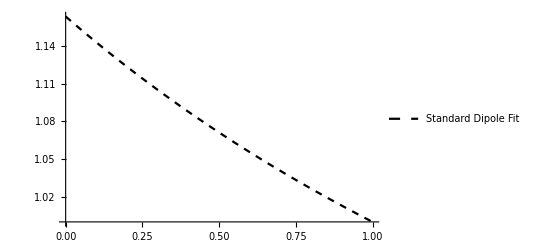

## Graph of R_(2γ) vs ε using suitable fit

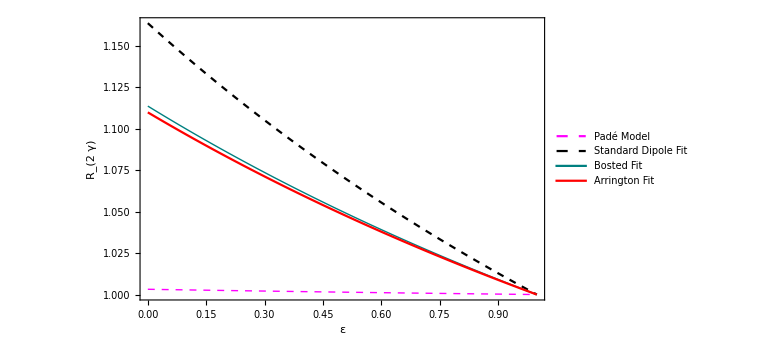

```mathematica
Show[PltBernauer,Dipoleplot,Pboosted,Parrington,PlotRange->All,Frame-> True,FrameTicks->All,FrameLabel->{Style["ε",Bold,18],Style["R_(2  γ)",Bold,18]},  ImageSize-> Large]
```

## VEPP-3 Experiment

```mathematica
CLASVEPP3=Import["F:\\Fahad Documents\\Dept. of Physics,SUST\\Study Materials\\4-2\\PROJECT PHY428-20220803T021501Z-001\\PROJECT PHY428\\Figures\\MATHEMATICA\\R_2gamma calculation\\VEPP-3\\VEPP-3 Data(Rachek 2015).csv"]
```

{{E_beam ,1.594,,0.998,},{epsilon,0.452,0.932,0.272,0.404},{Q^2,1.51,0.298,0.976,0.83},{R,1.0705,1.0037,1.0555,1.0447},{R_2gamma,1.0332,1.0002,1.0174,1.0133},{stat. error(R_2gamma),0.0112,0.0012,0.00049,0.0037},{sys. error(R_2gamma),0.0032,0.002,0.0016,0.0008}}

```mathematica
TableForm[CLASVEPP3]
```

E_beam  | 1.594 |  | 0.998 | 
epsilon | 0.452 | 0.932 | 0.272 | 0.404
Q^2 | 1.51 | 0.298 | 0.976 | 0.83
R | 1.0705 | 1.0037 | 1.0555 | 1.0447
R_2gamma | 1.0332 | 1.0002 | 1.0174 | 1.0133
stat. error(R_2gamma) | 0.0112 | 0.0012 | 0.00049 | 0.0037
sys. error(R_2gamma) | 0.0032 | 0.002 | 0.0016 | 0.0008

## E_Beam=1.594 GeV

```mathematica
epsdataV={0.452,0.932}
R2gammadataV={1.0332,1.0002}
R2gammaerrorV={0.0112,0.0012}
dataVEPP3=Transpose[{epsdataV, R2gammadataV}]
errorplotVEPP3= Transpose[{epsdataV, R2gammadataV, R2gammaerrorV}]
```

{0.452,0.932}

{1.0332,1.0002}

{0.0112,0.0012}

{{0.452,1.0332},{0.932,1.0002}}

{{0.452,1.0332,0.0112},{0.932,1.0002,0.0012}}

## Combined with CLAS data: Graph of R_(2γ) vs ε using suitable fit

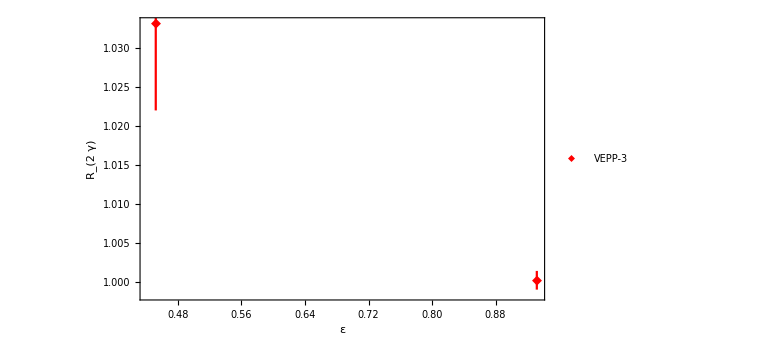

```mathematica
pltVEPP3=ErrorListPlot[Table[{errorplotVEPP3[[i,{1,2}]],ErrorBar[errorplotVEPP3[[i,3]]]},{i,1,Length[errorplotVEPP3]}], PlotStyle->Red,Joined->False,PlotMarkers->{"◆", Medium}, FrameLabel->{Style["ε",Bold,18],Style["R_(2  γ)",Bold,18]},PlotLegends-> Placed[LineLegend[{"VEPP-3"}],{0.75,0.95}], Frame-> True,FrameTicks->All,LabelStyle->Directive[FontFamily->"Arial",Bold,FontSize->14], ImageSize-> Large]
```

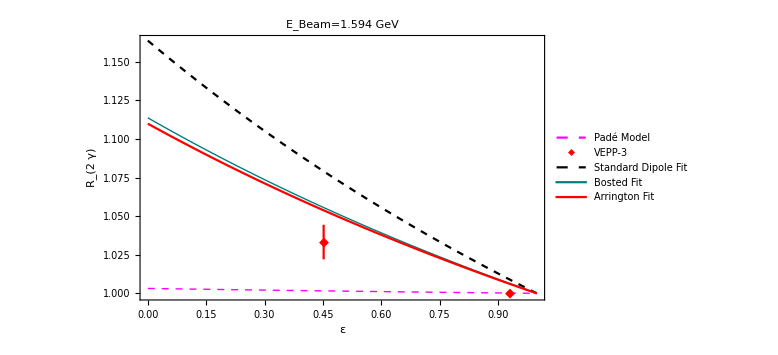

```mathematica
Show[PltBernauer,pltVEPP3,Dipoleplot,Pboosted,Parrington,PlotRange->All,Frame-> True,FrameTicks->All,PlotLabel->Style["E_Beam=1.594 GeV",Bold,Black],FrameLabel->{Style["ε",Bold,22,Black],Style["R_(2  γ)",Bold,20,Black]},Axes-> False,LabelStyle->Directive[FontFamily->"Arial",Bold,FontSize->14], FrameTicksStyle-> Directive[Black,14], ImageSize-> Large]
```